# Temporal-Semantic Journeys

## Rijksmuseum Semantic Explorer — Notebook 4 of 5

The Rijksmuseum collection spans centuries of artistic production, and many artworks carry date metadata. By combining embedding coordinates with these dates, we can trace how artistic style — as captured by the sentence transformer — evolves through time. This notebook computes period centroids, measures the rate of stylistic drift between consecutive eras, projects temporal trajectories onto PCA space, and identifies anachronistic artworks whose embeddings resemble a different century more than their own. The result is a quantitative, data-driven view of art history through the lens of semantic embeddings.

## 1. Data Loading

```mathematica
dataDir = FileNameJoin[{NotebookDirectory[], "data"}];
If[!DirectoryQ[dataDir],
  Print["Data not found. Run: uv run python export_for_mathematica.py"];
  Abort[]];
manifest = Import[FileNameJoin[{dataDir, "metadata.json"}], "RawJSON"];
{n, dim} = Lookup[manifest, {"n", "dim"}];
raw = BinaryReadList[FileNameJoin[{dataDir, "embeddings.bin"}], "Real32"];
embeddings = Partition[raw, dim];
artIds = manifest["art_ids"];
artworks = manifest["artworks"];
Print["Loaded ", n, " embeddings"]
```

Loaded 20000 embeddings

## 2. Temporal Coverage

Not all artworks in the collection carry date information, so we first assess coverage. The Rijksmuseum's holdings are heavily weighted towards the Dutch Golden Age (17th century) and the 19th century, reflecting the museum's historical collecting priorities. Artworks with both an earliest and latest date get a midpoint estimate; those with only one date use that value. Undated works are excluded from temporal analyses. The histogram reveals the temporal distribution and helps calibrate expectations: periods with very few artworks will produce noisier centroid estimates than well-represented ones.

```mathematica
(* Extract dates *)
dateEarliest = Table[artworks[ToString[id]]["date_earliest"], {id, artIds}];
dateLatest = Table[artworks[ToString[id]]["date_latest"], {id, artIds}];

(* Midpoint date *)
dateMid = MapThread[
  Which[
    NumberQ[#1] && NumberQ[#2], N[(#1 + #2) / 2],
    NumberQ[#1], N[#1],
    NumberQ[#2], N[#2],
    True, Null] &,
  {dateEarliest, dateLatest}];

(* Filter to dated artworks *)
datedMask = Flatten[Position[dateMid, _?NumberQ]];
datedDates = dateMid[[datedMask]];
datedEmbs = embeddings[[datedMask]];
datedIds = artIds[[datedMask]];
Print["Dated artworks: ", Length[datedMask], " / ", n,
  " (", NumberForm[100. Length[datedMask] / n, 3], "%)"]
```

Dated artworks: 19448 / 20000 (97.2%)

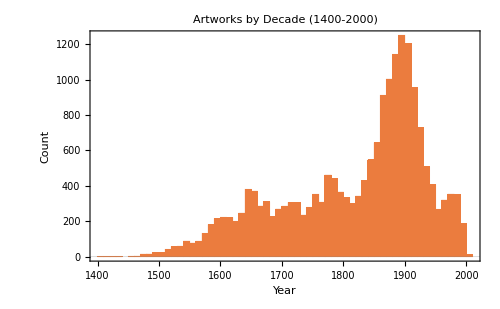
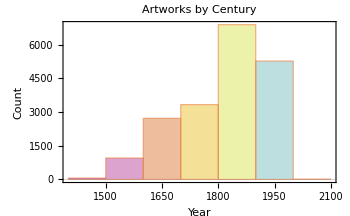

```mathematica
(* Date distribution *)
Row[{
  Histogram[Select[datedDates, 1400 <= # <= 2000 &], {10},
    PlotLabel -> "Artworks by Decade (1400-2000)",
    AxesLabel -> {"Year", "Count"},
    PlotTheme -> "Scientific",
    ImageSize -> 500],
  Spacer[20],
  Histogram[Select[datedDates, 1400 <= # <= 2000 &], {100},
    PlotLabel -> "Artworks by Century",
    AxesLabel -> {"Year", "Count"},
    ChartStyle -> "Pastel",
    PlotTheme -> "Scientific",
    ImageSize -> 350]
}]
```

## 3. Century-Level Style Centroids

The century centroid is the L2-normalised mean embedding of all dated artworks within a hundred-year window — a single vector summarising the typical semantic style of that era. Centuries with more artworks produce more robust centroids; we require at least 10 works per century to avoid noise. These centroids serve as reference points for all subsequent temporal analyses: we measure drift as the distance between them, build similarity matrices from their pairwise comparisons, and use them as baselines for the anachronism detection. The table shows which centuries are represented and how many artworks contribute to each centroid.

```mathematica
centuries = Table[c, {c, 1400, 1900, 100}];
centuryCentroids = Association[Table[
  Module[{mask, centuryEmbs},
    mask = Flatten[Position[datedDates, _?(c <= # < c + 100 &)]];
    If[Length[mask] >= 10,
      c -> <|"centroid" -> Normalize[Mean[datedEmbs[[mask]]]],
             "count" -> Length[mask]|>,
      Nothing]],
  {c, centuries}]];
centKeys = Keys[centuryCentroids];

Grid[
  Prepend[
    Table[{ToString[c] <> "s", centuryCentroids[c]["count"]}, {c, centKeys}],
    Style[#, Bold] & /@ {"Century", "Artworks"}],
  Frame -> All, Alignment -> Center,
  Background -> {None, {LightBlue, {White}}}]
```

Century | Artworks
1400s | 61
1500s | 955
1600s | 2726
1700s | 3333
1800s | 6896
1900s | 5276

## 4. Style Drift Over Time

Style drift is the cosine distance between the centroids of consecutive centuries — a single number summarising how much the average artistic style changed in that transition. Large jumps indicate periods of rapid transformation (perhaps driven by new technologies, cultural shifts, or colonial encounters), while small jumps indicate stylistic continuity. The drift plot gives an at-a-glance timeline of stylistic upheaval. Note that this measures shifts in the average, not in the diversity: a century could show low drift but high internal variation if its innovations cancelled out in the mean.

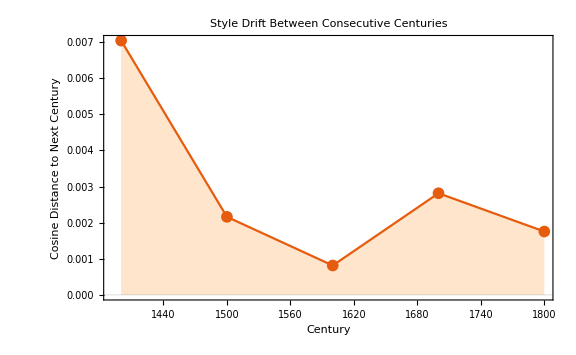

```mathematica
(* Inter-century cosine distances *)
drifts = Table[
  {centKeys[[i]], centKeys[[i + 1]],
   1 - centuryCentroids[centKeys[[i]]]["centroid"].centuryCentroids[centKeys[[i + 1]]]["centroid"]},
  {i, Length[centKeys] - 1}];

ListLinePlot[
  {#[[1]], #[[3]]} & /@ drifts,
  PlotLabel -> "Style Drift Between Consecutive Centuries",
  AxesLabel -> {"Century", "Cosine Distance to Next Century"},
  PlotMarkers -> {Automatic, 12},
  PlotTheme -> "Scientific",
  Filling -> Axis,
  FillingStyle -> Directive[Opacity[0.2], Orange],
  ImageSize -> Large]
```

## 5. Cross-Century Similarity

The cross-century similarity matrix shows cosine similarity between every pair of century centroids, revealing which eras produced semantically similar art even when separated by hundreds of years. Warm off-diagonal cells indicate unexpected temporal echoes — for instance, a 19th-century revival of 17th-century themes might show up as high similarity between those two rows. The diagonal is always 1.0 (each century is identical to itself). The overall pattern reveals whether artistic style follows a monotonic trajectory or cycles back to earlier forms.

```mathematica
centVecs = centuryCentroids[#]["centroid"] & /@ centKeys;
periodSimMat = Outer[Dot, centVecs, centVecs, 1];

MatrixPlot[periodSimMat,
  FrameTicks -> {
    {Thread[{Range[Length[centKeys]], ToString[#] <> "s" & /@ centKeys}], None},
    {Thread[{Range[Length[centKeys]], ToString[#] <> "s" & /@ centKeys}], None}},
  PlotLabel -> "Century-Level Style Similarity",
  ColorFunction -> "TemperatureMap",
  PlotLegends -> Automatic,
  ImageSize -> 500]
```

-Graphics-

## 6. Temporal Trajectory Through Embedding Space

By projecting period centroids onto the first two principal components of the full embedding space, we can visualise the path that artistic style traces through a 2D slice of the 384-dimensional space. Each point represents a 50-year window, and arrows connect consecutive periods to show the direction of drift. The colour gradient (purple to red) encodes time, making it easy to see whether the trajectory is roughly linear, curves back on itself, or shows sudden jumps. Century labels mark the major temporal landmarks. This trajectory is a compact visual summary of how the Rijksmuseum's holdings evolve semantically through the centuries.

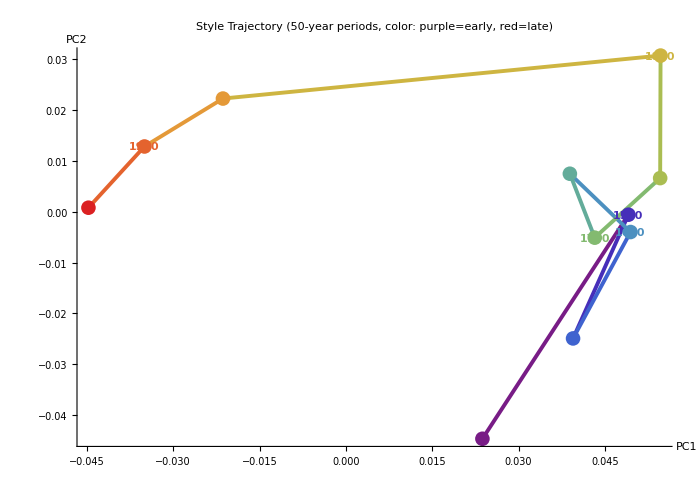

```mathematica
(* Compute global PCA basis *)
mu = Mean[embeddings];
centered = embeddings - ConstantArray[mu, n];
covMat = Transpose[centered].centered / (n - 1);
{eigenvalues, eigenvectors} = Eigensystem[covMat];
order = Reverse[Ordering[eigenvalues]];
eigenvectors = eigenvectors[[order]];
pcBasis2D = eigenvectors[[1 ;; 2]];

(* 50-year period centroids for smoother trajectory *)
periods = Table[p, {p, 1400, 1950, 50}];
periodCentroids = Association[Table[
  Module[{mask},
    mask = Flatten[Position[datedDates, _?(p <= # < p + 50 &)]];
    If[Length[mask] >= 10,
      p -> Normalize[Mean[datedEmbs[[mask]]]],
      Nothing]],
  {p, periods}]];
periodKeys = Keys[periodCentroids];

(* Project onto 2D PCA *)
periodProjected = Table[
  (periodCentroids[p] - mu).Transpose[pcBasis2D],
  {p, periodKeys}];

nPeriods = Length[periodKeys];
Graphics[{
  (* Trajectory arrows colored by time *)
  Table[
    {Thickness[0.004],
     ColorData["Rainbow"][(i - 1) / (nPeriods - 1)],
     Arrow[{periodProjected[[i]], periodProjected[[i + 1]]}]},
    {i, nPeriods - 1}],
  (* Points and labels *)
  Table[
    {PointSize[0.015],
     ColorData["Rainbow"][(i - 1) / (nPeriods - 1)],
     Point[periodProjected[[i]]],
     If[Mod[periodKeys[[i]], 100] == 0,
       Text[Style[ToString[periodKeys[[i]]], 11, Bold],
         periodProjected[[i]], {0, -1.8}],
       Nothing]},
    {i, nPeriods}]
  },
  Axes -> True,
  AxesLabel -> {"PC1", "PC2"},
  PlotLabel -> "Style Trajectory (50-year periods, color: purple=early, red=late)",
  ImageSize -> 700,
  AspectRatio -> 0.7]
```

## 7. Anachronism Detection

An anachronistic artwork is one whose embedding is more similar to the centroid of a different century than to its own era's centroid. Such works are stylistically 'out of time' — their semantic content resembles a different period more than the one in which they were created. This could reflect a deliberate archaism (copying older styles), a forward-looking innovation (anticipating future trends), or a misattributed date. The anomaly score is the difference between the similarity to the best-matching other century and the similarity to the artwork's own century: positive values mean the work is a better semantic fit for a different era.

```mathematica
(* For each dated artwork, compare similarity to own century vs best other century *)
datedCenturies = Floor[datedDates / 100] * 100;

anomalies = Table[
  Module[{ownCentury, sims, ownSim, bestOther},
    ownCentury = datedCenturies[[i]];
    If[!KeyExistsQ[centuryCentroids, ownCentury], Nothing,
      ownSim = datedEmbs[[i]].centuryCentroids[ownCentury]["centroid"];
      sims = Table[
        {c, datedEmbs[[i]].centuryCentroids[c]["centroid"]},
        {c, Select[centKeys, # != ownCentury &]}];
      bestOther = First[Reverse[SortBy[sims, Last]]];
      {bestOther[[2]] - ownSim, datedIds[[i]], ownCentury, bestOther[[1]], datedDates[[i]]}]],
  {i, Length[datedMask]}];
anomalies = Select[anomalies, Head[#] === List &];
anomalies = Reverse[SortBy[anomalies, First]];

Print[Style["Top 20 'Anachronistic' Artworks:", Bold]];
Print["(Most similar to a different century than their own)"];
Grid[
  Prepend[
    Table[
      Module[{a = anomalies[[i]], meta},
        meta = artworks[ToString[a[[2]]]];
        {StringTake[meta["title"], UpTo[45]],
         Round[a[[5]]],
         ToString[a[[3]]] <> "s",
         ToString[a[[4]]] <> "s",
         NumberForm[a[[1]], 3]}],
      {i, Min[20, Length[anomalies]]}],
    Style[#, Bold] & /@ {"Title", "Year", "Own Era", "Resembles", "Score"}],
  Frame -> All, Alignment -> {{Left, Center, Center, Center, Center}},
  Background -> {None, {LightOrange, {White}}}]
```

Top 20 'Anachronistic' Artworks:

(Most similar to a different century than their own)

Title | Year | Own Era | Resembles | Score
Portret van Joos de Damhouder | 1570 | 1500s | 1900s | 0.0234
Kustlandschap met landhuis | 1590 | 1500s | 1900s | 0.0221
Kaarsenkroon met zes armen en engel | 1850 | 1800s | 1400s | 0.0219
Zittende moeder met meisje | 1784 | 1700s | 1900s | 0.0211
Aanbidding der Koningen | 1920 | 1900s | 1500s | 0.0205
Strook kloskant met hangende bladtak | 1825 | 1800s | 1400s | 0.0204
Portret van Paul Eber | 1597 | 1500s | 1900s | 0.0201
Perseus en Andromeda | 1908 | 1900s | 1500s | 0.02
Perseus en het zeemonster | 1907 | 1900s | 1500s | 0.0197
Bloemstudie | 1716 | 1700s | 1900s | 0.0193
Kerstkaart met voorstellingen van de Apocalyp | 1953 | 1900s | 1500s | 0.0193
Portret van Guglielmo Gratarolo | 1587 | 1500s | 1800s | 0.019
Jacht op wilde katten | 1556 | 1500s | 1900s | 0.019
Mitaine van kloskant met c-voluten met zigzag | 1874 | 1800s | 1400s | 0.0184
Taneran aan de noordzijde | 1700 | 1700s | 1900s | 0.0184
Landschap | 1640 | 1600s | 1900s | 0.0182
Rond kleedje van achthoekig batist met rondom | 1912 | 1900s | 1400s | 0.0179
Boerderij aan een landweg | 1788 | 1700s | 1900s | 0.0179
Strook kloskant met twee composities van c-vo | 1860 | 1800s | 1400s | 0.0179
Kalligrafische tekst | 1750 | 1700s | 1900s | 0.0177

## 8. Style Velocity

Style velocity refines the century-level drift analysis by using finer 25-year windows, giving a higher-resolution view of when artistic style changed fastest. The velocity is computed as cosine distance between consecutive window centroids, normalised by the time interval (expressed per century for comparability). Peaks in the velocity curve mark periods of rapid stylistic innovation or disruption, while troughs mark periods of relative stability. The dashed horizontal line shows the mean velocity across all periods for reference. Comparing this curve against major art-historical events can validate whether the embedding model captures real stylistic shifts.

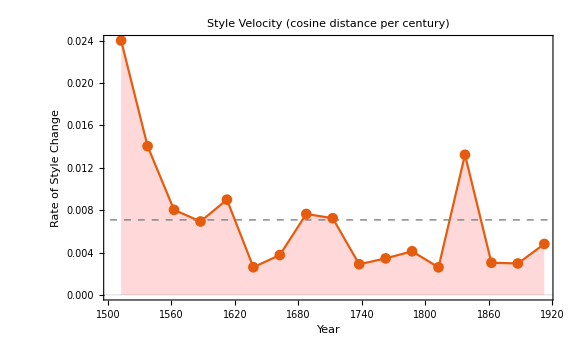

```mathematica
(* 25-year windows for velocity estimation *)
windows = Table[w, {w, 1500, 1925, 25}];
windowCentroids = Association[Table[
  Module[{mask},
    mask = Flatten[Position[datedDates, _?(w <= # < w + 25 &)]];
    If[Length[mask] >= 5,
      w -> Normalize[Mean[datedEmbs[[mask]]]],
      Nothing]],
  {w, windows}]];
windowKeys = Keys[windowCentroids];

(* Style velocity = cosine distance / time between consecutive windows *)
velocities = Table[
  Module[{dt = windowKeys[[i + 1]] - windowKeys[[i]]},
    {(windowKeys[[i]] + windowKeys[[i + 1]]) / 2,
     (1 - windowCentroids[windowKeys[[i]]].windowCentroids[windowKeys[[i + 1]]]) / (dt / 100)}],
  {i, Length[windowKeys] - 1}];

ListLinePlot[velocities,
  PlotLabel -> "Style Velocity (cosine distance per century)",
  AxesLabel -> {"Year", "Rate of Style Change"},
  PlotMarkers -> Automatic,
  Filling -> Axis,
  FillingStyle -> Directive[Opacity[0.15], Red],
  PlotTheme -> "Scientific",
  ImageSize -> Large,
  Epilog -> {Gray, Dashed,
    InfiniteLine[{0, Mean[velocities[[All, 2]]]}, {1, 0}]}]
```